```mathematica
SetDirectory[NotebookDirectory[]]
```

## Funciones

```mathematica
PuntosManuales[lista_, nombreArchivo_, plotear_]:=Module[{puntos},
puntos=DeleteDuplicates[lista];
Print[StringJoin[{"Longitud de lista ", ToString[Length[puntos]]}]];
Export[nombreArchivo,Append[puntos, "\n"], "Table"];
If[plotear==True, Show[ListPlot[puntos]],Unevaluated[Sequence[]]]

]

PuntosPaises[numpuntos_,pais_, nombreArchivo_, plotear_]:=Module[{n=numpuntos, n2, ℛ, pts}, 
n2=Round[n*1.8];
ℛ=DiscretizeGraphics[CountryData[pais,"Polygon"]];
pts=RandomPoint[ℛ,n2];
(*pts=Round[(pts/Abs[Min[pts]]+1)*n];*)
pts=Abs[pts];
pts=Round[(pts/Max[pts])*n];
pts=DeleteDuplicates[pts];
Print[StringJoin[{"Puntos disponibles ", ToString[Length[pts]], " Max: ", ToString[Max[pts]], " Min: ", ToString[Min[pts]]}]];
Export[nombreArchivo,Append[pts[[1;;n]], "\n"], "Table"];
Return[pts];
If[plotear==True, Show[ListPlot[pts[[1;;n]]]],Unevaluated[Sequence[]]]

]
GraficarConvexHull[archivoOriginales_, archivoCHull_, npuntos_]:=Module[{puntos, chull, p, ch, chL, plots, n},
puntos = Import[archivoOriginales, "Table"];
chull= Import[archivoCHull, "Table"];
chull = AppendTo[chull, chull[[1]]];
If[puntos[[-1]]=={}, puntos=Drop[puntos, -1], puntos=puntos];
If[npuntos==-1, n=Length[puntos], n=npuntos];
p=ListPlot[{puntos[[1;;n]]}, PlotStyle->{Blue, PointSize[Large]}]; 
ch=ListPlot[chull, PlotStyle->{Red, PointSize[Medium]}];
chL=ListPlot[chull, PlotStyle->{Red}, Joined->True];
plots={p,ch,chL};
Return[plots, Module];
Show[plots, ImageSize->Large]
]

GraficarChanConvexHull[archivoOriginales_, archivoCHull_, archivoFinal_, k_]:=Module[{name0=archivoOriginales, namef = archivoCHull, TPts, Mhulls, Tplots, nminis, i, fn0, Pts, fnf, FPts,p, ch, chL, arrPlot, ptsChan, plotFinal},
TPts={};
Mhulls={};
Tplots={};
nminis=0;
For[i=0,i<k,i++,
fn0=StringJoin[{name0, ToString[i],".txt"}];
Pts=Import[fn0, "Table"];
TPts=Append[TPts, Pts];
fnf=StringJoin[{namef, ToString[i],".txt"}];
FPts=Import[fnf, "Table"];
nminis=nminis+Length[FPts];
FPts = AppendTo[FPts, FPts[[1]]];
Mhulls=Append[Mhulls,FPts];

p=ListPlot[Pts, PlotStyle->{ColorData[96,i+1],PointSize[Large]}]; 
ch=ListPlot[FPts, PlotStyle->{Darker[ColorData[96,i+1]],PointSize[Medium]}];
chL=ListPlot[FPts, PlotStyle->{Darker[ColorData[96,i+1]]}, Joined->True];
arrPlot={p,ch,chL};
Tplots=Append[Tplots,arrPlot]
];
ptsChan=Import[archivoFinal, "Table"];
ptsChan= AppendTo[ptsChan, ptsChan[[1]]];
ch=ListPlot[ptsChan, PlotStyle->{Red,PointSize[Medium]}];
chL=ListPlot[ptsChan, PlotStyle->{Red}, Joined->True];
Return[{Tplots, ch, chL}, Module];
Show[Tplots,ch, chL, PlotRange->All]

]
```

```mathematica
PuntosManuales::usage="PuntosManuales[lista de puntos, nombre del archivo, ¿graficar?(True/False)]\nExportar archivo de texto con pares de puntos a partir de una lista.";
PuntosPaises::usage="PuntosPaises[número de puntos, str(país), nombre del archivo, ¿graficar?(True/False)]\nExportar archivo de texto con pares de puntos aleatorios según el territorio en 2D de un país.";
GraficarConvexHull::usage = "GraficarConvexHull[nombre de archivo original, nombre de archivo de puntos del Hull, número de puntos a leer]\nImportar archivos de puntos originales y puntos del Convex Hull y regresar un gráfico. Usar Show[<>] para mostrar gráfico resultante.";
GraficarChanConvexHull::usage="GraficarChanConvexHull[nombre de archivos individualescon puntos, nombre de archivos individuales con puntos del Hull, nombre del archivo con Hull final, k grupos de mini Hulls]\nPara los primeros dos archivos solo se da el nombre principal (sin extensión), automáticamente se enumeran según los k grupos; incluir nombre completo para el tercer archivo. Se graficarán los mini Convex Hull, y el final con el algoritmo de Chan, usar Show[<>] para mostrar gráfico resultante.";
```

## Código

```mathematica
pts={{2,14},{8,14},{5,11},{6,19},{8,15},{5,15},{5,17},{3,19},{8,12},{3,14},{4,12},{3,16},{11,17},{15,19},{19,16},{17,16},{10,14},{12,15},{5,13},{9,16},{13,12},{14,14},{6,16},{15,17},{12,17},{9,11},{11,11},{15,10},{16,9},{13,7},{11,9},{17,13},{16,13},{10,8},{13,9},{15,12},{9,1},{14,5},{13,6},{9,4},{10,7},{6,7},{11,5},{5,3},{7,5},{14,10},{9,6},{8,7}};
PuntosManuales[pts, "./puntos_manuales.txt",True]
```

```mathematica
pais=PuntosPaises[1000, "Mexico", "./puntos_china_1k.txt", False]
```

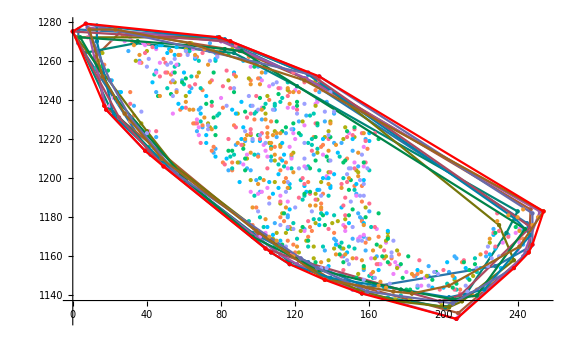

```mathematica
Todo=GraficarChanConvexHull["./puntos_originales_","./puntos_chull_","puntos_chull_final.txt",10];
Show[Todo, PlotRange->All, ImageSize->Large] (*Aun no existen esos archivos*)
```

```mathematica
?GraficarConvexHull
```

GraficarConvexHull[nombre de archivo original, nombre de archivo de puntos del Hull, número de puntos a leer]
Importar archivos de puntos originales y puntos del Convex Hull y regresar un gráfico. Usar Show[<>] para mostrar gráfico resultante.

```mathematica
?PuntosManuales
```

PuntosManuales[lista de puntos, nombre del archivo, ¿graficar?(True/False)]
Exportar archivo de texto con pares de puntos a partir de una lista.

```mathematica
?PuntosPaises
```

PuntosPaises[número de puntos, str(país), nombre del archivo, ¿graficar?(True/False)]
Exportar archivo de texto con pares de puntos aleatorios según el territorio en 2D de un país.

```mathematica
?GraficarChanConvexHull
```

GraficarChanConvexHull[nombre de archivos individualescon puntos, nombre de archivos individuales con puntos del Hull, nombre del archivo con Hull final, k grupos de mini Hulls]
Para los primeros dos archivos solo se da el nombre principal (sin extensión), automáticamente se enumeran según los k grupos; incluir nombre completo para el tercer archivo. Se graficarán los mini Convex Hull, y el final con el algoritmo de Chan, usar Show[<>] para mostrar gráfico resultante.